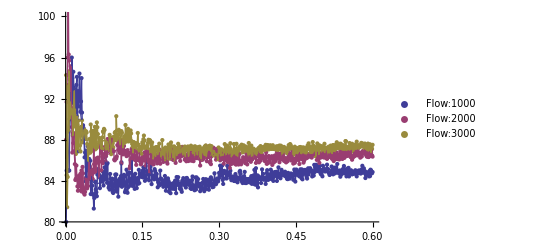

```mathematica
Num=3;
aver=Table[
Import["/Users/xuhao/Develop/modeling/highway/src/data/aver"<>ToString[i]<>".txt","Table"]
,{i,1,Num}];
Legen=Table[
"Flow:"<>ToString[i*1000],{i,1,Num}
];
p1=ListPlot[aver,PlotLegends->Legen,PlotRange->{80,100}];
Funcs=Map[Fit[#,Table[x^i,{i,0,20}],x]&,aver];
p2=Plot[Funcs,{x,0,0.6},PlotStyle->{Thickness[0.002]}];
Show[p1,p2,ListLinePlot[aver,ImageSize->Full,PlotRange->Full],ImageSize->Full]
```